# Neural Network Proof of Concept

## Noah Halford

A neural network to learn a randomly generated 16-element table; mostly adapted from pages 100-101 of the course script.

```mathematica
tableToLearn = Table[Random[Real,{0,1}],{i,1,9}]
```

{0.273107,0.959098,0.495778,0.547096,0.69809,0.755088,0.320536,0.159128,0.762712}

```mathematica
pairs =Flatten[ Table[{{i,j},tableToLearn[[j+3*(i-1)]]},{i,1,3},{j,1,3}],1]
```

{{{1,1},0.273107},{{1,2},0.959098},{{1,3},0.495778},{{2,1},0.547096},{{2,2},0.69809},{{2,3},0.755088},{{3,1},0.320536},{{3,2},0.159128},{{3,3},0.762712}}

```mathematica
inputs = 2; hidden=3;outnum=1;weights = Table[Table[Random[Real,{-0.1,0.1}],{inputs}],{hidden}]
hiddenweights=Table[Table[Random[Real,{-0.1,0.1}],{hidden}],{outnum}];
```

{{-0.083299,-0.0233762},{-0.017493,-0.00949759},{0.0243915,-0.0125624}}

```mathematica
step=0.05;
sigmoid[x_] :=1/(1 + Exp[-x]);
```

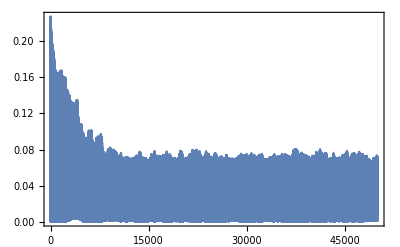

```mathematica
errors = Table[{in,t}=pairs[[Random[Integer,{1,9}]]];
outhid=sigmoid[weights.in];
out=sigmoid[hiddenweights.outhid];
err=t-out;
outdelta=err*out(1-out);
hiddelta=outhid(1-outhid) Transpose[wo].outdelta;
hiddenweights += step *Outer[Times,outdelta,outhid];
weights+= step* Outer[Times,hiddelta,in];
{err.err,wo,wh},{k,1,50000}];
ListPlot[errors[[All,1]],Joined->True,Frame->True,PlotRange->All]
```